# Library generation

Measure the public library generator and its individual stages. All libraries are written under an owned benchmark run directory; shipped libraries are never overwritten.

## 1. Load in a fresh kernel

Restart the kernel before switching between this generator notebook and notebooks 01–05. Rule definitions are memoised: first observations are recorded separately, but shared caches may already have been populated by earlier cases. No caches are cleared.

```mathematica
setupSeconds=First[AbsoluteTiming[setup=Get[FileNameJoin[{NotebookDirectory[],"Support","GeneratorBenchmark.wl"}]];]];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynGrav library generator — CalcFormConverter
Loading preserves Directory[] and starts no calculation, FORM check or installation.
Use CheckGravitonScalars (without brackets) to list libraries; GenerateGravitonScalarsSpecific[1] generates one order, and GenerateGravitonScalars[n] generates a batch.
Default library destination: /home/latosh/.Wolfram/Applications/FeynGrav/Libs/. Use OutputDirectory -> anExistingDirectory to generate elsewhere. Existing files are replaced only after validation.
All generation commands always print library and calculation-stage progress. FORMThreads chooses the worker count; ShowTiming -> True adds detailed timings.
Calculation defaults: automatic FORM/TFORM selection, up to eight TFORM workers with serial fallback if TFORM is missing; Dirac and colour processing enabled.
Pure/quadratic gravity: order n means n + 2 graviton legs. Gauss-Bonnet batches start at two; n = 1 returns Null without files.
Use ?function and Options[function] for signatures, defaults and failures. Full guide: /home/latosh/.Wolfram/Applications/FeynGrav/Libs/Generator.md
To suppress this introduction, set $FeynGravLibrariesGeneratorStartupMessage = False before loading.

## 2. Choose a profile and configuration

```mathematica
config=BenchmarkConfiguration[];
config["Profile"]="Full";
config["GeneratorThreads"]=Automatic;
cleanupSuccessfulFiles=False;
```

Choose "Quick" or "Full" explicitly. Quick measures scalar, fermion and vector generation at order one. Full adds order two and representative general-relativity, Yang–Mills, quadratic-gravity, Horndeski and Gauss–Bonnet cases. Axion cases, unresolved G5 cases and Gauss–Bonnet above order three are excluded. The helper section covers ITensor, CTensorGeneral without external pairs, and ETensor.

GeneratorThreads selects one configuration, not a scaling sweep: Automatic prefers up to eight TFORM workers with serial fallback. Use 1 for serial FORM. FORMExecutable and TFORMExecutable accept explicit paths; automatic threads with an explicit serial path select one worker, and an explicit TFORM path uses up to eight. Explicit multiworker requests do not fall back. OutputDirectory is a parent for a unique run directory. PhysicalRepetitions defaults to 1/3 and Repetitions to 3/5 in Quick/Full. ExecutionTimeout is 60/600 seconds per FORM execution only; it does not bound Mathematica evaluation or the entire run.

## 3. Prepare and inspect the environment

```mathematica
prepared=If[FailureQ[setup],setup,BenchmarkPrepare["Generation",config]];
If[AssociationQ[prepared],prepared["SetupSeconds"]=setupSeconds;];
```

Checking the selected FORM configuration; no rule expression is constructed in preparation.

```mathematica
BenchmarkEnvironment[prepared]
```

Profile | Full
Wolfram | 15.0.1 for Linux x86 (64-bit) (July 2, 2026)
FeynCalc | 10.2.1
FORM | 5.0.2
Executable | /usr/local/bin/tform
Workers | 8
Generation repetitions | 3
Helper repetitions | 5
FORM timeout (seconds) | 600

Preparation checks executables but does not construct generation inputs. Missing FORM skips generation while helper measurements remain usable. Nothing installs software. Every prepared run may execute once; prepare again for another run.

## 4. Measure sequentially

```mathematica
report=BenchmarkRun[prepared];
```

Each public command runs first: first observation, one warmup, then measured repetitions, each with fresh output paths. Its isolated construction, export, execution, import, writing/read-back and publication stages follow. Multi-file public commands are timed together; staged rows identify each library. A progress bar shows completed cases and the current stage. Detailed progress is saved in progress.log in the run directory. Logging remains part of public-command timing.

## 5. Inspect validation and timings

```mathematica
StandardForm[BenchmarkSummary[report]]
```

Case | Stage | Workers | Trials | MeanSeconds | MedianSeconds
GravitonScalars[1] | Generate | 8 | 3 | 0.178559 | 0.176406
GravitonScalarVertex_1 | Construction | 8 | 3 | 0.000159667 | 0.00015
GravitonScalarVertex_1 | Export | 8 | 3 | 0.00544367 | 0.005363
GravitonScalarVertex_1 | Execute | 8 | 3 | 0.033683 | 0.0337
GravitonScalarVertex_1 | Import | 8 | 3 | 0.00629133 | 0.00633
GravitonScalarVertex_1 | WriteVerify | 8 | 3 | 0.000758333 | 0.00075
GravitonScalarVertex_1 | Publish | 8 | 3 | 0.000169667 | 0.000169
GravitonScalarVertex_1 | StageSum | 8 | 3 | 0.0465057 | 0.046526
GravitonScalarPotentialVertex_1 | Construction | 8 | 3 | 0.0000366667 | 0.000035
GravitonScalarPotentialVertex_1 | Export | 8 | 3 | 0.004817 | 0.00473
GravitonScalarPotentialVertex_1 | Execute | 8 | 3 | 0.0328067 | 0.032945
GravitonScalarPotentialVertex_1 | Import | 8 | 3 | 0.00547167 | 0.005521
GravitonScalarPotentialVertex_1 | WriteVerify | 8 | 3 | 0.000505333 | 0.000516
GravitonScalarPotentialVertex_1 | Publish | 8 | 3 | 0.00018 | 0.000179
GravitonScalarPotentialVertex_1 | StageSum | 8 | 3 | 0.0438173 | 0.043496
GravitonFermions[1] | Generate | 8 | 3 | 0.108732 | 0.107901
GravitonFermionVertex_1 | Construction | 8 | 3 | 0.0000843333 | 0.000084
GravitonFermionVertex_1 | Export | 8 | 3 | 0.0232193 | 0.023211
GravitonFermionVertex_1 | Execute | 8 | 3 | 0.033466 | 0.033469
GravitonFermionVertex_1 | Import | 8 | 3 | 0.013898 | 0.013858
GravitonFermionVertex_1 | WriteVerify | 8 | 3 | 0.000955667 | 0.000955
GravitonFermionVertex_1 | Publish | 8 | 3 | 0.000196667 | 0.000196
GravitonFermionVertex_1 | StageSum | 8 | 3 | 0.07182 | 0.071813
GravitonVectors[1] | Generate | 8 | 3 | 0.28825 | 0.287903
GravitonMassiveVectorVertex_1 | Construction | 8 | 3 | 0.000167333 | 0.000173
GravitonMassiveVectorVertex_1 | Export | 8 | 3 | 0.00846733 | 0.008588
GravitonMassiveVectorVertex_1 | Execute | 8 | 3 | 0.034261 | 0.034272
GravitonMassiveVectorVertex_1 | Import | 8 | 3 | 0.00929733 | 0.009301
GravitonMassiveVectorVertex_1 | WriteVerify | 8 | 3 | 0.00164333 | 0.001631
GravitonMassiveVectorVertex_1 | Publish | 8 | 3 | 0.000195667 | 0.000196
GravitonMassiveVectorVertex_1 | StageSum | 8 | 3 | 0.054032 | 0.054126
GravitonVectorVertex_1 | Construction | 8 | 3 | 0.0000713333 | 0.000071
GravitonVectorVertex_1 | Export | 8 | 3 | 0.00924933 | 0.009286
GravitonVectorVertex_1 | Execute | 8 | 3 | 0.034039 | 0.034078
GravitonVectorVertex_1 | Import | 8 | 3 | 0.0111883 | 0.011241
GravitonVectorVertex_1 | WriteVerify | 8 | 3 | 0.002305 | 0.002287
GravitonVectorVertex_1 | Publish | 8 | 3 | 0.000197667 | 0.000195
GravitonVectorVertex_1 | StageSum | 8 | 3 | 0.0570507 | 0.05701
GravitonVectorGhostVertex_1 | Construction | 8 | 3 | 0.0000483333 | 0.000048
GravitonVectorGhostVertex_1 | Export | 8 | 3 | 0.00714333 | 0.007103
GravitonVectorGhostVertex_1 | Execute | 8 | 3 | 0.0343473 | 0.03434
GravitonVectorGhostVertex_1 | Import | 8 | 3 | 0.00779933 | 0.007928
GravitonVectorGhostVertex_1 | WriteVerify | 8 | 3 | 0.000741333 | 0.000742
GravitonVectorGhostVertex_1 | Publish | 8 | 3 | 0.000203667 | 0.000207
GravitonVectorGhostVertex_1 | StageSum | 8 | 3 | 0.0502833 | 0.050358
GravitonScalars[2] | Generate | 8 | 3 | 0.200346 | 0.197925
GravitonScalarVertex_2 | Construction | 8 | 3 | 0.000194 | 0.000193
GravitonScalarVertex_2 | Export | 8 | 3 | 0.0109493 | 0.010775
GravitonScalarVertex_2 | Execute | 8 | 3 | 0.035178 | 0.035239
GravitonScalarVertex_2 | Import | 8 | 3 | 0.0132363 | 0.013201
GravitonScalarVertex_2 | WriteVerify | 8 | 3 | 0.002212 | 0.002209
GravitonScalarVertex_2 | Publish | 8 | 3 | 0.000209333 | 0.000205
GravitonScalarVertex_2 | StageSum | 8 | 3 | 0.061979 | 0.061895
GravitonScalarPotentialVertex_2 | Construction | 8 | 3 | 0.0000626667 | 0.000061
GravitonScalarPotentialVertex_2 | Export | 8 | 3 | 0.00853467 | 0.008569
GravitonScalarPotentialVertex_2 | Execute | 8 | 3 | 0.035741 | 0.035175
GravitonScalarPotentialVertex_2 | Import | 8 | 3 | 0.009899 | 0.009845
GravitonScalarPotentialVertex_2 | WriteVerify | 8 | 3 | 0.000842667 | 0.000841
GravitonScalarPotentialVertex_2 | Publish | 8 | 3 | 0.000213333 | 0.000212
GravitonScalarPotentialVertex_2 | StageSum | 8 | 3 | 0.0552933 | 0.054698
GravitonFermions[2] | Generate | 8 | 3 | 0.2709 | 0.272697
GravitonFermionVertex_2 | Construction | 8 | 3 | 0.000324333 | 0.000324
GravitonFermionVertex_2 | Export | 8 | 3 | 0.13867 | 0.139946
GravitonFermionVertex_2 | Execute | 8 | 3 | 0.0359973 | 0.035946
GravitonFermionVertex_2 | Import | 8 | 3 | 0.0608557 | 0.061263
GravitonFermionVertex_2 | WriteVerify | 8 | 3 | 0.00547833 | 0.005483
GravitonFermionVertex_2 | Publish | 8 | 3 | 0.000223333 | 0.000228
GravitonFermionVertex_2 | StageSum | 8 | 3 | 0.241549 | 0.242822
GravitonVectors[2] | Generate | 8 | 3 | 0.432496 | 0.431333
GravitonMassiveVectorVertex_2 | Construction | 8 | 3 | 0.000195 | 0.000195
GravitonMassiveVectorVertex_2 | Export | 8 | 3 | 0.0215243 | 0.021178
GravitonMassiveVectorVertex_2 | Execute | 8 | 3 | 0.0367157 | 0.036478
GravitonMassiveVectorVertex_2 | Import | 8 | 3 | 0.0276197 | 0.027616
GravitonMassiveVectorVertex_2 | WriteVerify | 8 | 3 | 0.009634 | 0.009568
GravitonMassiveVectorVertex_2 | Publish | 8 | 3 | 0.000216 | 0.000218
GravitonMassiveVectorVertex_2 | StageSum | 8 | 3 | 0.0959047 | 0.09561
GravitonVectorVertex_2 | Construction | 8 | 3 | 0.000359 | 0.000357
GravitonVectorVertex_2 | Export | 8 | 3 | 0.0494187 | 0.049396
GravitonVectorVertex_2 | Execute | 8 | 3 | 0.0369197 | 0.037387
GravitonVectorVertex_2 | Import | 8 | 3 | 0.047063 | 0.046937
GravitonVectorVertex_2 | WriteVerify | 8 | 3 | 0.0240403 | 0.024089
GravitonVectorVertex_2 | Publish | 8 | 3 | 0.000219333 | 0.00022
GravitonVectorVertex_2 | StageSum | 8 | 3 | 0.15802 | 0.158614
GravitonVectorGhostVertex_2 | Construction | 8 | 3 | 0.0000756667 | 0.000076
GravitonVectorGhostVertex_2 | Export | 8 | 3 | 0.0130963 | 0.013094
GravitonVectorGhostVertex_2 | Execute | 8 | 3 | 0.0369157 | 0.037337
GravitonVectorGhostVertex_2 | Import | 8 | 3 | 0.015634 | 0.015661
GravitonVectorGhostVertex_2 | WriteVerify | 8 | 3 | 0.00202967 | 0.002024
GravitonVectorGhostVertex_2 | Publish | 8 | 3 | 0.000214 | 0.000214
GravitonVectorGhostVertex_2 | StageSum | 8 | 3 | 0.0679653 | 0.068405
GravitonVertex[1] | Generate | 8 | 3 | 0.186042 | 0.185882
GravitonVertex_1 | Construction | 8 | 3 | 0.000112333 | 0.000111
GravitonVertex_1 | Export | 8 | 3 | 0.0335353 | 0.033657
GravitonVertex_1 | Execute | 8 | 3 | 0.0366533 | 0.036302
GravitonVertex_1 | Import | 8 | 3 | 0.048752 | 0.048399
GravitonVertex_1 | WriteVerify | 8 | 3 | 0.025361 | 0.02508
GravitonVertex_1 | Publish | 8 | 3 | 0.000228667 | 0.000225
GravitonVertex_1 | StageSum | 8 | 3 | 0.144643 | 0.144783
GravitonSUNYM[1] | Generate | 8 | 3 | 1.18382 | 1.17967
GravitonQuarkGluonVertex_1 | Construction | 8 | 3 | 0.000315 | 0.00031
GravitonQuarkGluonVertex_1 | Export | 8 | 3 | 0.0626673 | 0.063217
GravitonQuarkGluonVertex_1 | Execute | 8 | 3 | 0.0373117 | 0.036674
GravitonQuarkGluonVertex_1 | Import | 8 | 3 | 0.03857 | 0.038145
GravitonQuarkGluonVertex_1 | WriteVerify | 8 | 3 | 0.00106167 | 0.001036
GravitonQuarkGluonVertex_1 | Publish | 8 | 3 | 0.000227333 | 0.000226
GravitonQuarkGluonVertex_1 | StageSum | 8 | 3 | 0.140153 | 0.141552
GravitonGluonVertex_1 | Construction | 8 | 3 | 0.000129 | 0.000129
GravitonGluonVertex_1 | Export | 8 | 3 | 0.0907853 | 0.090674
GravitonGluonVertex_1 | Execute | 8 | 3 | 0.037898 | 0.037165
GravitonGluonVertex_1 | Import | 8 | 3 | 0.0573303 | 0.057984
GravitonGluonVertex_1 | WriteVerify | 8 | 3 | 0.002933 | 0.002959
GravitonGluonVertex_1 | Publish | 8 | 3 | 0.000231333 | 0.000235
GravitonGluonVertex_1 | StageSum | 8 | 3 | 0.189307 | 0.18877
GravitonThreeGluonVertex_1 | Construction | 8 | 3 | 0.000109667 | 0.000106
GravitonThreeGluonVertex_1 | Export | 8 | 3 | 0.100245 | 0.100104
GravitonThreeGluonVertex_1 | Execute | 8 | 3 | 0.0389813 | 0.039383
GravitonThreeGluonVertex_1 | Import | 8 | 3 | 0.06515 | 0.065269
GravitonThreeGluonVertex_1 | WriteVerify | 8 | 3 | 0.00522633 | 0.005239
GravitonThreeGluonVertex_1 | Publish | 8 | 3 | 0.000229333 | 0.000231
GravitonThreeGluonVertex_1 | StageSum | 8 | 3 | 0.209942 | 0.210356
GravitonFourGluonVertex_1 | Construction | 8 | 3 | 0.000112667 | 0.000116
GravitonFourGluonVertex_1 | Export | 8 | 3 | 0.087452 | 0.087507
GravitonFourGluonVertex_1 | Execute | 8 | 3 | 0.0387623 | 0.038755
GravitonFourGluonVertex_1 | Import | 8 | 3 | 0.081714 | 0.08111
GravitonFourGluonVertex_1 | WriteVerify | 8 | 3 | 0.013745 | 0.013776
GravitonFourGluonVertex_1 | Publish | 8 | 3 | 0.000225333 | 0.000225
GravitonFourGluonVertex_1 | StageSum | 8 | 3 | 0.222011 | 0.220429
GravitonYMGhostVertex_1 | Construction | 8 | 3 | 0.000077 | 0.000073
GravitonYMGhostVertex_1 | Export | 8 | 3 | 0.0647873 | 0.063482
GravitonYMGhostVertex_1 | Execute | 8 | 3 | 0.0387057 | 0.038737
GravitonYMGhostVertex_1 | Import | 8 | 3 | 0.0380937 | 0.03809
GravitonYMGhostVertex_1 | WriteVerify | 8 | 3 | 0.001008 | 0.001013
GravitonYMGhostVertex_1 | Publish | 8 | 3 | 0.00023 | 0.000229
GravitonYMGhostVertex_1 | StageSum | 8 | 3 | 0.142902 | 0.14165
GravitonGluonGhostVertex_1 | Construction | 8 | 3 | 0.000116333 | 0.000117
GravitonGluonGhostVertex_1 | Export | 8 | 3 | 0.0731417 | 0.073546
GravitonGluonGhostVertex_1 | Execute | 8 | 3 | 0.03798 | 0.037953
GravitonGluonGhostVertex_1 | Import | 8 | 3 | 0.0430003 | 0.043227
GravitonGluonGhostVertex_1 | WriteVerify | 8 | 3 | 0.00129567 | 0.001268
GravitonGluonGhostVertex_1 | Publish | 8 | 3 | 0.000239 | 0.00024
GravitonGluonGhostVertex_1 | StageSum | 8 | 3 | 0.155773 | 0.156994
QuadraticGravityVertex[1] | Generate | 8 | 3 | 0.705366 | 0.701358
QuadraticGravityVertex_1 | Construction | 8 | 3 | 0.000183667 | 0.000184
QuadraticGravityVertex_1 | Export | 8 | 3 | 0.142052 | 0.141067
QuadraticGravityVertex_1 | Execute | 8 | 3 | 0.0837407 | 0.082968
QuadraticGravityVertex_1 | Import | 8 | 3 | 0.174975 | 0.175175
QuadraticGravityVertex_1 | WriteVerify | 8 | 3 | 0.249955 | 0.249913
QuadraticGravityVertex_1 | Publish | 8 | 3 | 0.000239333 | 0.000236
QuadraticGravityVertex_1 | StageSum | 8 | 3 | 0.651146 | 0.651117
QuadraticGravityVertex[2] | Generate | 8 | 3 | 26.2914 | 26.142
QuadraticGravityVertex_2 | Construction | 8 | 3 | 0.000472333 | 0.000488
QuadraticGravityVertex_2 | Export | 8 | 3 | 2.50473 | 2.5014
QuadraticGravityVertex_2 | Execute | 8 | 3 | 2.98659 | 2.93932
QuadraticGravityVertex_2 | Import | 8 | 3 | 7.29436 | 7.38942
QuadraticGravityVertex_2 | WriteVerify | 8 | 3 | 17.1944 | 17.2648
QuadraticGravityVertex_2 | Publish | 8 | 3 | 0.000340667 | 0.000339
QuadraticGravityVertex_2 | StageSum | 8 | 3 | 29.9809 | 30.0612
ScalarGaussBonnet[2] | Generate | 8 | 3 | 0.197923 | 0.197046
ScalarGaussBonnet_2 | Construction | 8 | 3 | 0.0000916667 | 0.000092
ScalarGaussBonnet_2 | Export | 8 | 3 | 0.033017 | 0.033196
ScalarGaussBonnet_2 | Execute | 8 | 3 | 0.0527363 | 0.053084
ScalarGaussBonnet_2 | Import | 8 | 3 | 0.0418253 | 0.039697
ScalarGaussBonnet_2 | WriteVerify | 8 | 3 | 0.00519833 | 0.005172
ScalarGaussBonnet_2 | Publish | 8 | 3 | 0.000288333 | 0.000289
ScalarGaussBonnet_2 | StageSum | 8 | 3 | 0.133157 | 0.131921
ScalarGaussBonnet[3] | Generate | 8 | 3 | 0.644429 | 0.644576
ScalarGaussBonnet_3 | Construction | 8 | 3 | 0.000114667 | 0.000117
ScalarGaussBonnet_3 | Export | 8 | 3 | 0.0960283 | 0.095995
ScalarGaussBonnet_3 | Execute | 8 | 3 | 0.05242 | 0.052706
ScalarGaussBonnet_3 | Import | 8 | 3 | 0.254279 | 0.256321
ScalarGaussBonnet_3 | WriteVerify | 8 | 3 | 0.182763 | 0.182729
ScalarGaussBonnet_3 | Publish | 8 | 3 | 0.000285667 | 0.000283
ScalarGaussBonnet_3 | StageSum | 8 | 3 | 0.585891 | 0.584837
HorndeskiG2[0,2,1] | Generate | 8 | 3 | 0.216959 | 0.216311
HorndeskiG2_0_2_1 | Construction | 8 | 3 | 0.000165667 | 0.000165
HorndeskiG2_0_2_1 | Export | 8 | 3 | 0.059604 | 0.060053
HorndeskiG2_0_2_1 | Execute | 8 | 3 | 0.051886 | 0.051012
HorndeskiG2_0_2_1 | Import | 8 | 3 | 0.0381657 | 0.037973
HorndeskiG2_0_2_1 | WriteVerify | 8 | 3 | 0.00263567 | 0.002637
HorndeskiG2_0_2_1 | Publish | 8 | 3 | 0.000290667 | 0.000291
HorndeskiG2_0_2_1 | StageSum | 8 | 3 | 0.152748 | 0.152338
HorndeskiG3[0,1,1] | Generate | 8 | 3 | 0.212982 | 0.212867
HorndeskiG3_0_1_1 | Construction | 8 | 3 | 0.000101 | 0.0001
HorndeskiG3_0_1_1 | Export | 8 | 3 | 0.0458147 | 0.045929
HorndeskiG3_0_1_1 | Execute | 8 | 3 | 0.0529333 | 0.053745
HorndeskiG3_0_1_1 | Import | 8 | 3 | 0.048227 | 0.046002
HorndeskiG3_0_1_1 | WriteVerify | 8 | 3 | 0.003363 | 0.003321
HorndeskiG3_0_1_1 | Publish | 8 | 3 | 0.000314333 | 0.00031
HorndeskiG3_0_1_1 | StageSum | 8 | 3 | 0.150753 | 0.149185
HorndeskiG4[0,1,1] | Generate | 8 | 3 | 0.23912 | 0.243733
HorndeskiG4_0_1_1 | Construction | 8 | 3 | 0.000130333 | 0.000132
HorndeskiG4_0_1_1 | Export | 8 | 3 | 0.0487433 | 0.048413
HorndeskiG4_0_1_1 | Execute | 8 | 3 | 0.0546017 | 0.052617
HorndeskiG4_0_1_1 | Import | 8 | 3 | 0.0452393 | 0.045502
HorndeskiG4_0_1_1 | WriteVerify | 8 | 3 | 0.00340533 | 0.003442
HorndeskiG4_0_1_1 | Publish | 8 | 3 | 0.000324667 | 0.000333
HorndeskiG4_0_1_1 | StageSum | 8 | 3 | 0.152445 | 0.14976
HorndeskiG5[2,0,1] | Generate | 8 | 3 | 0.221078 | 0.217478
HorndeskiG5_2_0_1 | Construction | 8 | 3 | 0.00009 | 0.00009
HorndeskiG5_2_0_1 | Export | 8 | 3 | 0.0457757 | 0.04458
HorndeskiG5_2_0_1 | Execute | 8 | 3 | 0.053078 | 0.053189
HorndeskiG5_2_0_1 | Import | 8 | 3 | 0.0440503 | 0.04413
HorndeskiG5_2_0_1 | WriteVerify | 8 | 3 | 0.002981 | 0.002967
HorndeskiG5_2_0_1 | Publish | 8 | 3 | 0.000311333 | 0.000313
HorndeskiG5_2_0_1 | StageSum | 8 | 3 | 0.146286 | 0.145416
ITensor pairs=1 | Helper | 0 | 5 | 0.0000486 | 0.000049
ITensor pairs=2 | Helper | 0 | 5 | 0.0000586 | 0.00006
ITensor pairs=3 | Helper | 0 | 5 | 0.0000696 | 0.000068
ITensor pairs=4 | Helper | 0 | 5 | 0.0000808 | 0.00008
CTensorGeneral pairs=1 | Helper | 0 | 5 | 0.0000496 | 0.000049
CTensorGeneral pairs=2 | Helper | 0 | 5 | 0.0000612 | 0.000058
CTensorGeneral pairs=3 | Helper | 0 | 5 | 0.0000702 | 0.00007
CTensorGeneral pairs=4 | Helper | 0 | 5 | 0.0000834 | 0.000082
ETensor pairs=1 | Helper | 0 | 5 | 0.0000644 | 0.000064
ETensor pairs=2 | Helper | 0 | 5 | 0.0000736 | 0.000073
ETensor pairs=3 | Helper | 0 | 5 | 0.0000838 | 0.000079
ETensor pairs=4 | Helper | 0 | 5 | 0.0000934 | 0.000094

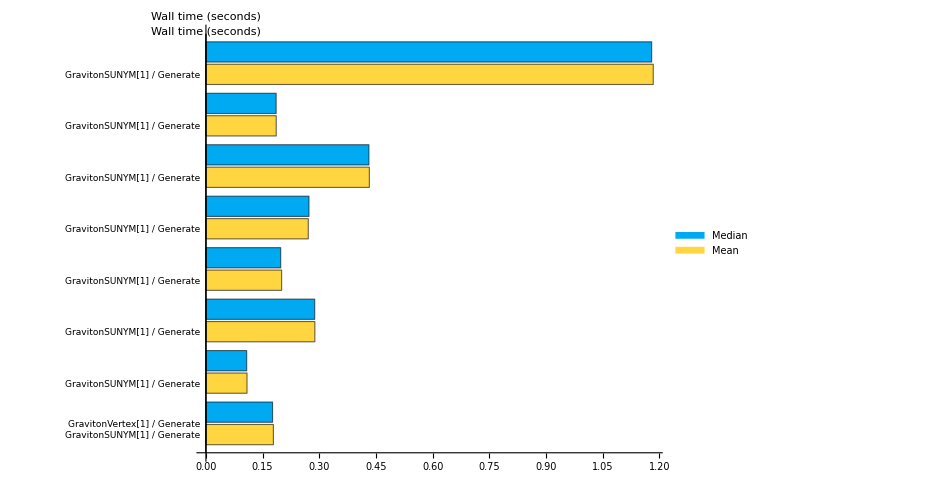
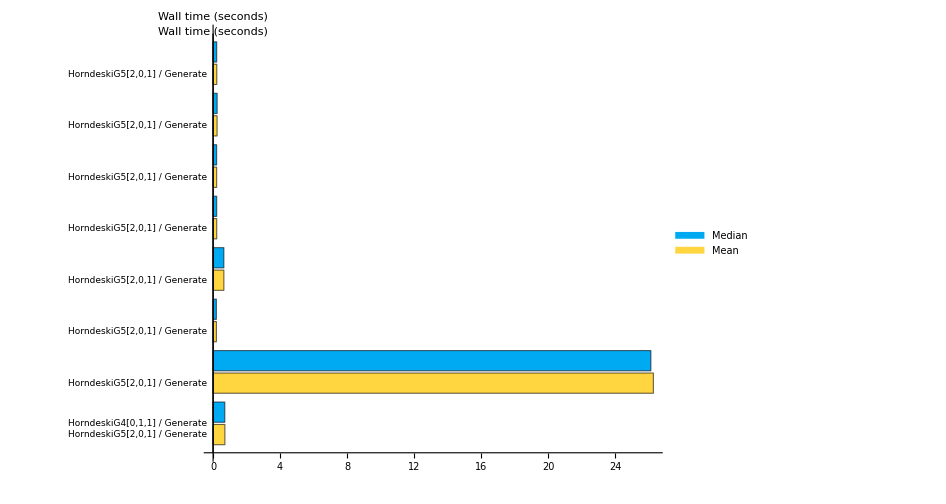
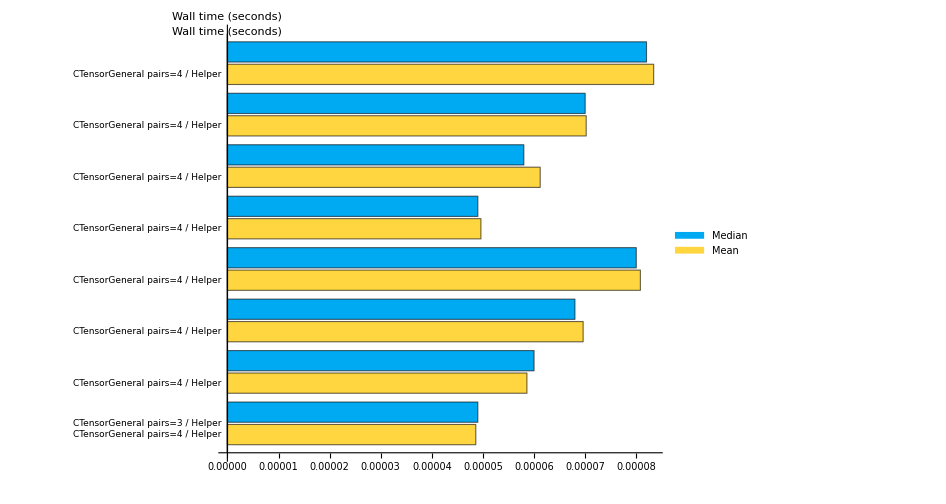
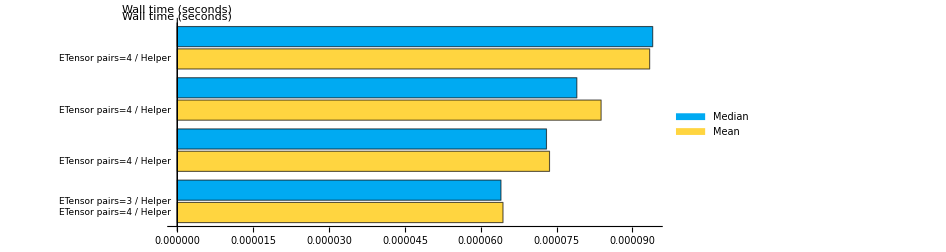
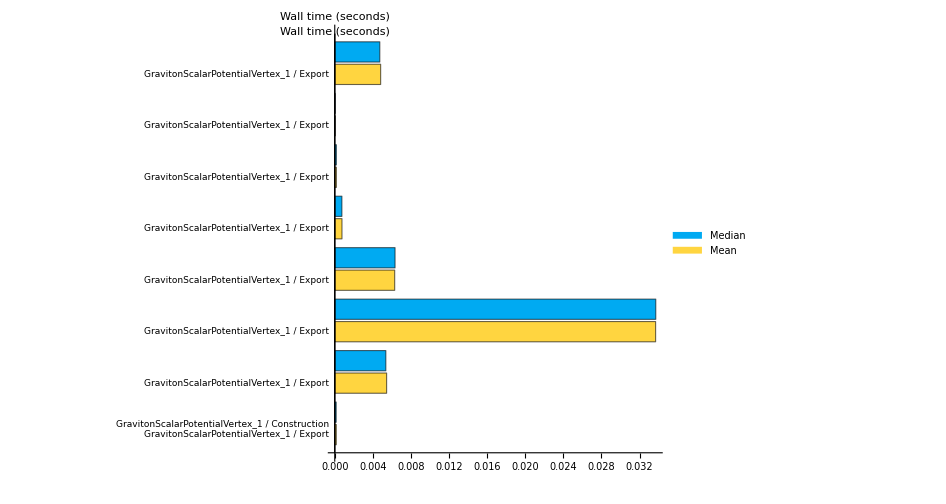
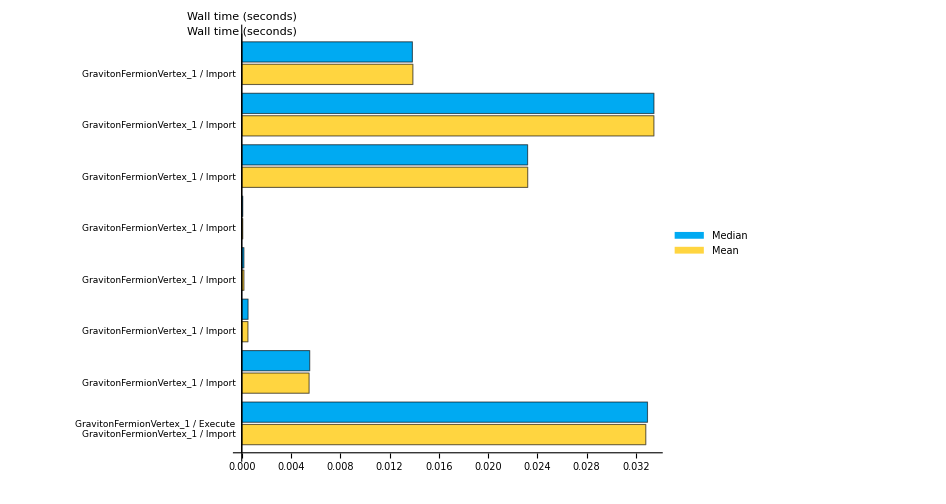
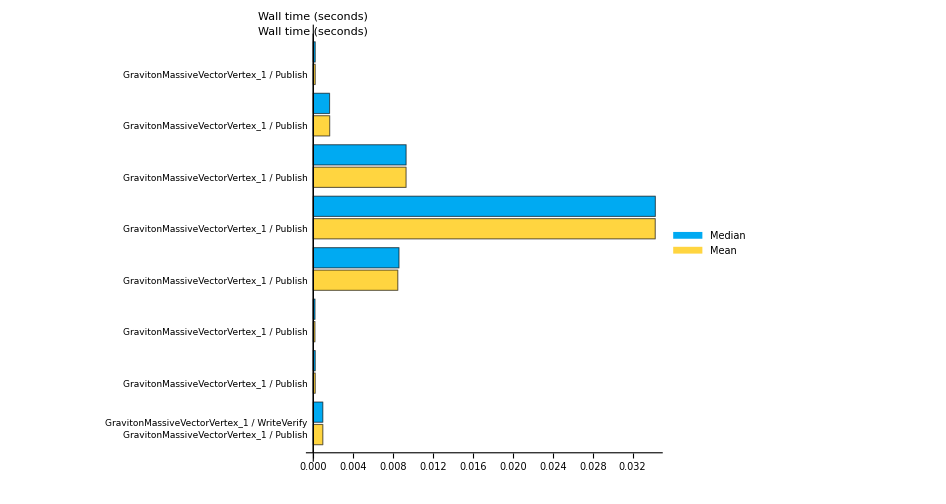
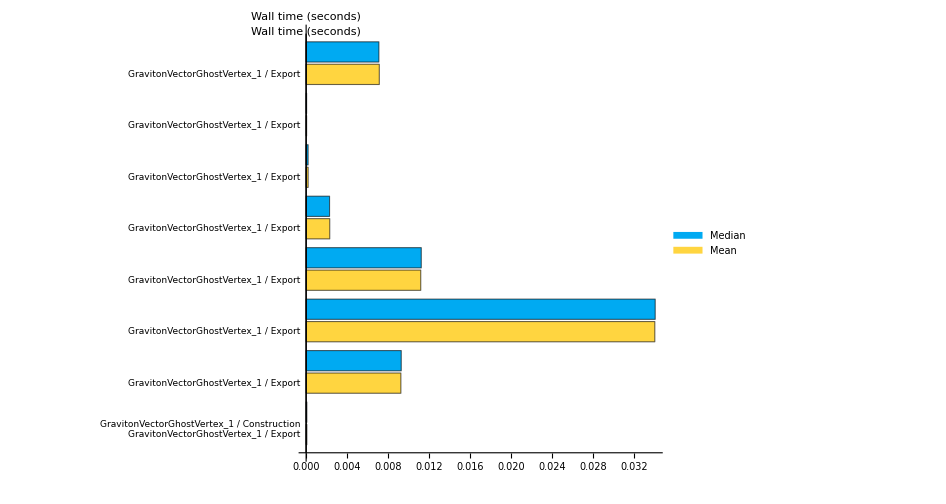
Public command totals
-Graphics-
-Graphics-
Supplementary tensors
-Graphics-
-Graphics-
Individual stages
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
BenchmarkPlot[report]
```

```mathematica
BenchmarkDiagnostics[report]
```

No failed or inconclusive observations.

Mean and median include successful measured observations only. First observations and warmups are excluded. File presence and readability are checked; no comparison with earlier expressions is performed. Raw observations remain in JSON. With one trial the mean and median coincide.

## 6. Interpret and retain results

All measurements use wall time. StageSum includes the six isolated stages and is not the public Generate total: these are different executions with different cache histories and bookkeeping. Export/import, validation and fingerprints are not part of Execute. Repeated calls use memoised rules; these results do not predict a fresh-kernel construction time. Filesystem caches, background load and temperature affect timings. No cross-machine speedup is guaranteed.

```mathematica
If[AssociationQ[report],report["Directory"]]
```

/tmp/generator-benchmark-7f2627dd-0256-46fd-8a54-c8b93fa25da4

JSON records provenance, raw rows, file fingerprints, sizes and diagnostics; CSV contains validated timing summaries. Observations are checkpointed. Reports and failed-job files survive optional cleanup. Choose a persistent output parent if the reports should survive temporary-directory cleanup.

```mathematica
If[TrueQ[cleanupSuccessfulFiles]&&AssociationQ[report],BenchmarkCleanup[report]]
```